# Why the Wolfram Language for anatomy?

## Dr Juan H Klopper

## Reasons

There are so many reason that it will be impossible to list them here.  We could, though, look at some of the important ones:

This notebook form

Biostatistics

Healthcare information

Anatomical data

3D anatomical plots

## Biostatistics

```mathematica
SeedRandom[1]
groupA=RandomVariate[NormalDistribution[120,10],100];
groupB=RandomVariate[NormalDistribution[130,20],100];
```

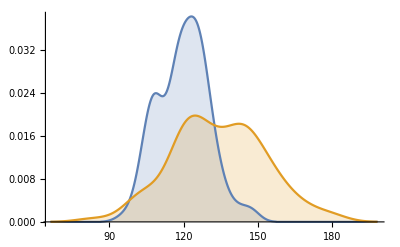

```mathematica
SmoothHistogram[{groupA,groupB},Filling->Axis]
```

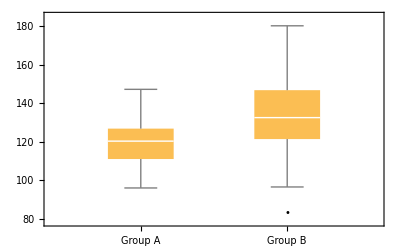

```mathematica
BoxWhiskerChart[{groupA,groupB},"Outliers",ChartLabels->{"Group A","Group B"}]
```

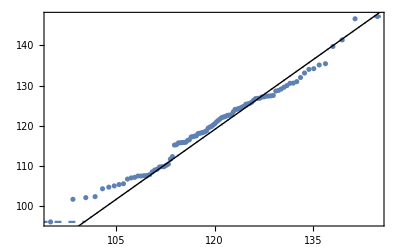

```mathematica
QuantilePlot[groupA]
```

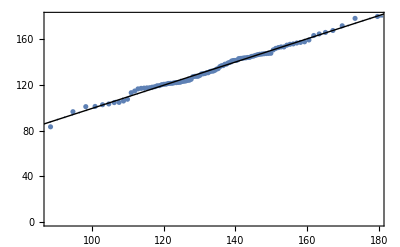

```mathematica
QuantilePlot[groupB]
```

```mathematica
ShapiroWilkTest[groupA]
```

0.294186

```mathematica
ShapiroWilkTest[groupB]
```

0.824109

```mathematica
TTest[{groupA,groupB},0,{"TestDataTable","TestConclusion"}]
```

{ | Statistic | P-Value
T | -6.66669 | 4.48435×10^-10,The null hypothesis that the mean difference is 0 is rejected at the 5 percent level based on the T test.}

## Healthcare information

```mathematica
EntityValue[Entity["AnatomicalStructure","Pancreas"],"Function"]
```

secretes insulin and glucagon into the bloodstream to control blood sugar level, and secretes pancreatic enzymes into small intestine to break down ingested materials for absorption

Nutritional content of a banana

WolframAlphaQueryResults

Population of the United States of America since 2000

WolframAlphaQueryResults

## Anatomical data

```mathematica
AnatomyData[Entity["AnatomicalStructure","BicepsBrachii"],"MuscleAction"]
```

{{elbow,flexion},{forearm,supination},{shoulder,flexion}}

```mathematica
AnatomyData[Entity["AnatomicalStructure","BicepsBrachii"],{"MuscleAction","MuscleAntagonist","MuscleOrigin","MuscleInsertion"}]
```

{{{elbow,flexion},{forearm,supination},{shoulder,flexion}},{triceps brachii},{coracoid process,supraglenoid tubercle,apical part of coracoid process},{radial tuberosity,antebrachial fascia}}

## 3D anatomy plots

```mathematica
AnatomyPlot3D[{Orange,Entity["AnatomicalStructure","RightAtrium"],Blue,Entity["AnatomicalStructure","LeftAtrium"],Yellow,Entity["AnatomicalStructure","RightVentricle"],Red,Entity["AnatomicalStructure","LeftVentricle"],Entity["AnatomicalStructure","CoronaryArtery"],Blue,Entity["AnatomicalStructure","LeftInferiorPulmonaryVein"],Red,Entity["AnatomicalStructure","PulmonaryTrunk"],Pink,LinguisticAssistant,Green,Entity["AnatomicalStructure","Trachea"],Green,Entity["AnatomicalStructure","SetOfBronchi"],Red,Entity["AnatomicalStructure","ThyroidGland"]}]
```

-Graphics3D-